```mathematica
R[z_]:=(1+5z/12)/(1-7z/12+z^2/12)
```

```mathematica
bd=Table[{((7+5Exp[-I θ])+√((7+5Exp[-I θ])^2-4(12(1-Exp[-I θ]))))/2,((7+5Exp[-I θ])-√((7+5Exp[-I θ])^2-4(12(1-Exp[-I θ]))))/2},{θ,0,2π,2π/30}]//Flatten;
```

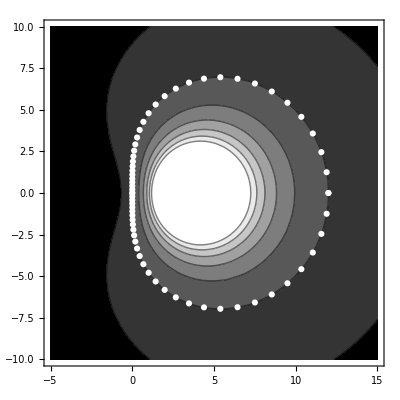

```mathematica
Show[{
ContourPlot[Norm[R[x+I y]],{x,-5,15},{y,-10,10},ColorFunction->GrayLevel],ListPlot[{Re[bd],Im[bd]}//Transpose,PlotRange->{{-5,15},{-10,10}},PlotStyle->White]
}]
```

```mathematica
RR[z_] = (1/3(4((1+z/4)/(1-z/4))-1))/(1-z/3)
```

(-1+(4 (1+z/4))/(1-z/4))/(3 (1-z/3))

```mathematica
RR[z]==R[z]//FullSimplify
```

ⅇ^(ⅈ θ)==(12+5 z)/(12-7 z+z^2)

```mathematica
(-1+(4 (1+z/4))/(1-z/4))/(3 (1-z/3))//FullSimplify
```

(12+5 z)/(12-7 z+z^2)

```mathematica
DSolve[{D[x[t],t]==-x[t]^3/3+x[t]+a[t],D[a[t],t]==-ϵ x[t],x[0]==2,a[0]==2/3},{x[t],a[t]},t]
```

DSolve[{x'[t]==a[t]+x[t]-x[t]^3/3,a'[t]==-ϵ x[t],x[0]==2,a[0]==2/3},{x[t],a[t]},t]

```mathematica
Limit[(1+k l)(1+2k l)^n,{k->0}]
```

1

```mathematica
Solve[x^2-2x z-1==0,x]
```

{{x→z-√(1+z^2)},{x→z+√(1+z^2)}}

```mathematica
Solve[{η==c1+c2,(1+z)η==c1(z-√(1+z^2))+c2(z+√(1+z^2))},{c1,c2}]
```

{{c1→((-1+√(1+z^2)) η)/(2 √(1+z^2)),c2→((1+√(1+z^2)) η)/(2 √(1+z^2))}}

```mathematica
U[n_] = ((-1+√(1+z^2)) η)/(2 √(1+z^2))(z-√(1+z^2))^n+((1+√(1+z^2)) η)/(2 √(1+z^2))(z+√(1+z^2))^n
```

((z-√(1+z^2))^n (-1+√(1+z^2)) η)/(2 √(1+z^2))+((1+√(1+z^2)) (z+√(1+z^2))^n η)/(2 √(1+z^2))

```mathematica
U[3]//FullSimplify
```

(1+2 z) (1+z+2 z^2) η

```mathematica
Limit[U[n],{z->0}]2
```

η

```mathematica
Manipulate[Plot[x^2-2x+3-z(x-2)(x-3),{x,-10,10}],{z,0,100}]
```

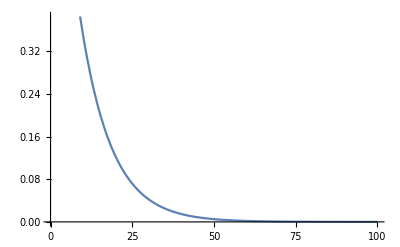

```mathematica
Plot[(1-.1)^n,{n,0,100}]
```